```mathematica
yyyHankSingle[x_,y_,t_,k_,w_]:=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t])/(11),{d,-12,12,2.4}]
```

```mathematica
yyyHankSingle[x,y,t,k,w]
```

1/11 (BesselJ[0,k √(x^2+(-12.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-12.+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(-9.6+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-9.6+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(-7.2+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-7.2+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(-4.8+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-4.8+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(-2.4+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-2.4+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(0.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(0.+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(2.4+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(2.4+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(4.8+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(4.8+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(7.2+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(7.2+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(9.6+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(9.6+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(12.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(12.+y)^2)] Sin[t w])

```mathematica
DaForceSingleX[x_,y_,t_,k_,w_] = -D[yyyHankSingle[x,y,t,k,w],x];
DaForceSingleY[x_,y_,t_,k_,w_] = -D[yyyHankSingle[x,y,t,k,w],y];
CosDisSqWidth = ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]
GaussianTanDisSqWidth[d_,σ_] = ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]
SincSqWidth[d_] = ProbabilityDistribution[Sinc[x π/(d)]^2/d,{x,-π/2,π/2}]
```

ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]

ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]

ProbabilityDistribution[Sinc[(x π)/d]^2/d,{x,-π/2,π/2}]

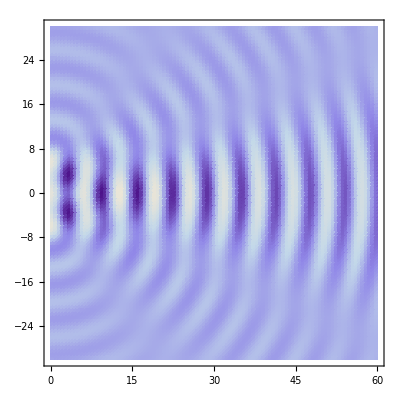

```mathematica
DensityPlot[yyyHankSingle[x,y,0,1,1],{x,0,60},{y,-30,30},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

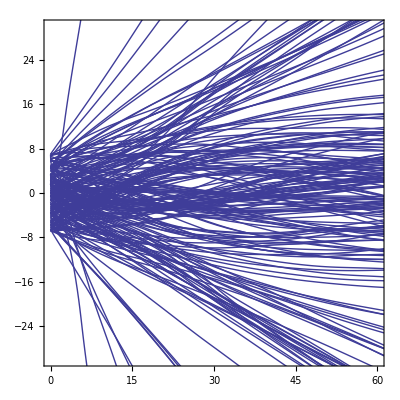

```mathematica
AAA =  1.0;
ddd = 7.0;
x000 = 0.0;
www=1;
v000 = 1.0;
kkk= 1;
disss = 0.005;
tmax = 100;
xmax = 60;
NMAX=200;
phase = - π;

Hollandtabl3DU=
Parallelize[
Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}]
];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA =  1.0;
WIDTHVALUE =12;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 200;
swidth = 1;
phase = -π;
CHUNK = 100;
REPEAT = 100;
CUTTOFF = 160;
WIDTHLIST = {2,4,6,8,10};



Close["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitC160W"<> ToString[WIDTHVALUE]<>".dat"]



Do[

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitC160W"<> ToString[WIDTHVALUE]<>".dat"];

Hollandtabl3DU=
Parallelize[Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-WIDTHVALUE,WIDTHVALUE}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth ]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}]
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]
,{REPEAT}];
```

General::openx: "/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitC160W12.dat" is not open.

Close[/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitC160W12.dat]

$Aborted